-Graphics-

-Graphics-

```mathematica
pic:=Module[{},
Print[Graphics[{
Line[{{-.1,-.1},{-.1,depth+.1},{width+.1,depth+.1},{width+.1,-.1},{-.1,-.1}}],
Table[arrow[i,j],{i,1,width},{j,1,depth}]
},AspectRatio->Automatic,ImageSize->40 (width+.22),PlotRange->{{-.11,width+.11},{-.11,depth+.11}}]];
Print[Graphics[{Table[Text[StyleForm[solns[[1]][[i,j]],FontSize->20],{i-1/2,j-1/2}],{i,1,width},{j,1,depth}],
Line[{{-.1,-.1},{-.1,depth+.1},{width+.1,depth+.1},{width+.1,-.1},{-.1,-.1}}],
Table[arrow[i,j],{i,1,width},{j,1,depth}]
},AspectRatio->Automatic,ImageSize->40 (width+.22),PlotRange->{{-.11,width+.11},{-.11,depth+.11}}]];]
```

```mathematica
pic:=Module[{},
Print[Graphics[{
Line[{{-.1,-.1},{-.1,depth+.1},{width+.1,depth+.1},{width+.1,-.1},{-.1,-.1}}],
Table[arrow[i,j],{i,1,width},{j,1,depth}]
},AspectRatio->Automatic,ImageSize->40 (width+.3),PlotRange->{{-.15,width+.15},{-.15,depth+.15}}]];
Print[Graphics[{
Line[{{-.1,-.1},{-.1,depth+.1},{width+.1,depth+.1},{width+.1,-.1},{-.1,-.1}}],
Table[Which[solns[[1]][[i,j]]==1,arrow[i,j],True,{Brown,arrow[i,j]/.Line->Polygon,Black,arrow[i,j]}],{i,1,width},{j,1,depth}]
},AspectRatio->Automatic,ImageSize->40 (width+.3),PlotRange->{{-.15,width+.15},{-.15,depth+.15}}]];]
```

```mathematica
Graphics[{Brown,arrow[1,2]/.Line->Polygon,Black,arrow[1,2]}]
```

```mathematica
arrow[i_,j_]:={
Which[directions[[i,j]]==1,Line[{{i-.9,j-.6},{i-.65,j-.35},{i-.8,j-.2},{i-.2,j-.2},{i-.2,j-.8},{i-.35,j-.65},{i-.6,j-.9},{i-.9,j-.6}}],
directions[[i,j]]==2,Line[{{i-.7,j-.9},{i-.7,j-.5},{i-.9,j-.5},{i-.5,j-.1},{i-.1,j-.5},{i-.3,j-.5},{i-.3,j-.9},{i-.7,j-.9}}],
directions[[i,j]]==3,Line[{{i-.1,j-.6},{i-.35,j-.35},{i-.2,j-.2},{i-.8,j-.2},{i-.8,j-.8},{i-.65,j-.65},{i-.4,j-.9},{i-.1,j-.6}}],
directions[[i,j]]==4,Line[{{i-.1,j-.7},{i-.5,j-.7},{i-.5,j-.9},{i-.9,j-.5},{i-.5,j-.1},{i-.5,j-.3},{i-.1,j-.3},{i-.1,j-.7}}],
directions[[i,j]]==5,Line[{{i-.1,j-.4},{i-.35,j-.65},{i-.2,j-.8},{i-.8,j-.8},{i-.8,j-.2},{i-.65,j-.35},{i-.4,j-.1},{i-.1,j-.4}}],
directions[[i,j]]==6,Line[{{i-.7,j-.1},{i-.7,j-.5},{i-.9,j-.5},{i-.5,j-.9},{i-.1,j-.5},{i-.3,j-.5},{i-.3,j-.1},{i-.7,j-.1}}],
directions[[i,j]]==7,Line[{{i-.9,j-.4},{i-.65,j-.65},{i-.8,j-.8},{i-.2,j-.8},{i-.2,j-.2},{i-.35,j-.35},{i-.6,j-.1},{i-.9,j-.4}}],
directions[[i,j]]==8,Line[{{i-.9,j-.7},{i-.5,j-.7},{i-.5,j-.9},{i-.1,j-.5},{i-.5,j-.1},{i-.5,j-.3},{i-.9,j-.3},{i-.9,j-.7}}]]
}
```

```mathematica
DD:=Table[Which[
i==(width+1)/2&&j==(depth+1)/2,Random[Integer,{1,8}],
i<(width+1)/2&&j==(depth+1)/2,Mod[Random[Integer,{5,9}],8]+1,
i>(width+1)/2&&j==(depth+1)/2,Random[Integer,{2,6}],
i==(width+1)/2&&j<(depth+1)/2,Mod[Random[Integer,{7,11}],8]+1,
i==(width+1)/2&&j>(depth+1)/2,Random[Integer,{4,8}],
i≤width/2&&j≤depth/2,Mod[Random[Integer,{7,9}],8]+1,
i≤width/2,Random[Integer,{6,8}],
j≤depth/2,Random[Integer,{2,4}],
True,Random[Integer,{4,6}]],{i,1,width},{j,1,depth}]
```

```mathematica
pointsat[i_,j_]:=Which[
directions[[i,j]]==2,Table[{i,k},{k,j+1,depth}],
directions[[i,j]]==6,Table[{i,k},{k,1,j-1}],
directions[[i,j]]==4,Table[{k,j},{k,1,i-1}],
directions[[i,j]]==8,Table[{k,j},{k,i+1,width}],
directions[[i,j]]==1,Table[{i+k,j+k},{k,1,Min[width-i,depth-j]}],
directions[[i,j]]==7,Table[{i+k,j-k},{k,1,Min[width-i,j-1]}],
directions[[i,j]]==5,Table[{i-k,j-k},{k,1,Min[i-1,j-1]}],
directions[[i,j]]==3,Table[{i-k,j+k},{k,1,Min[i-1,depth-j]}]]
```

```mathematica
check[c_]:=Apply[And,Flatten[Table[correct[i,j,c],{i,1,width},{j,1,depth}]]]
```

```mathematica
correct[i_,j_,c_]:=Module[{},
temp=Map[c[[Apply[Sequence,#]]]&,pointsat[i,j]];
If[c[[i,j]]>0&&Apply[And,Map[#>0&,temp]],If[c[[i,j]]==1,Total[temp-1]==1,Total[2-temp]==2],True]] (* one 2 and two 1's *)
```

```mathematica
correct[i_,j_,c_]:=Module[{},
temp=Map[c[[Apply[Sequence,#]]]&,pointsat[i,j]];
If[c[[i,j]]>0&&Apply[And,Map[#>0&,temp]],If[c[[i,j]]==1,Count[temp,1]==1,Count[temp,2]==2],True]] 
(* 1->1 and 2->2 *)
```

```mathematica
correct[i_,j_,c_]:=Module[{},
temp=Map[c[[Apply[Sequence,#]]]&,pointsat[i,j]];
If[c[[i,j]]>0&&Apply[And,Map[#>0&,temp]],If[c[[i,j]]==1,Count[temp,2]==1,If[c[[i,j]]==2,Count[temp,3]==2,Count[temp,1]==3||Count[temp,2]==3]],True]] 
(* one 1,2,3 *)
```

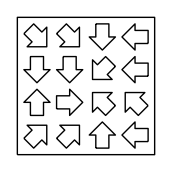

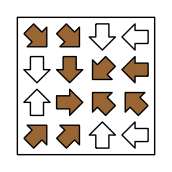

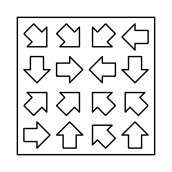

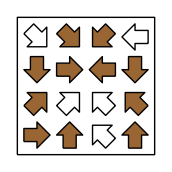

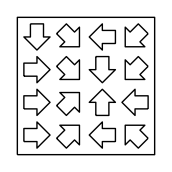

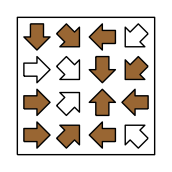

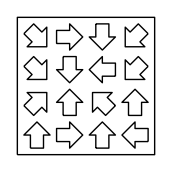

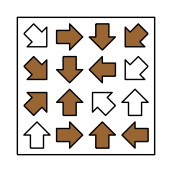

$Aborted

```mathematica
width=4;
depth=4;
For[p=1,p>0,p++,
directions=DD;
solns={};
stac={Table[0,{width},{depth}]};
While[Length[stac]>0&&Length[solns]<2,
top=First[stac];
stac=Rest[stac];
next=Position[top,0];
If[next=={},AppendTo[solns,top],
next=First[next];
x=next[[1]];y=next[[2]];
If[check[ReplacePart[top,next->1]],PrependTo[stac,ReplacePart[top,next->1]]];
If[check[ReplacePart[top,next->2]],PrependTo[stac,ReplacePart[top,next->2]]]]];
If[Length[solns]==1,pic]]
```

```mathematica
width=5;
depth=5;
For[p=1,p>0,p++,
directions=DD;
solns={};
stac={Table[0,{width},{depth}]};
While[Length[stac]>0&&Length[solns]<2,
top=First[stac];
stac=Rest[stac];
next=Position[top,0];
If[next=={},AppendTo[solns,top],
next=First[next];
x=next[[1]];y=next[[2]];
If[check[ReplacePart[top,next->1]],PrependTo[stac,ReplacePart[top,next->1]]];
If[check[ReplacePart[top,next->2]],PrependTo[stac,ReplacePart[top,next->2]]];
If[check[ReplacePart[top,next->3]],PrependTo[stac,ReplacePart[top,next->3]]]]];
Print[Length[solns]];
If[Length[solns]==1,pic]]
```

## 1-->2-->1 - 4x4

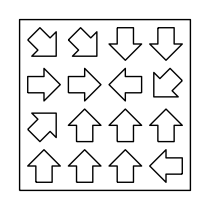

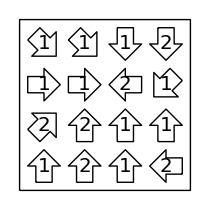

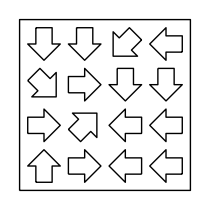

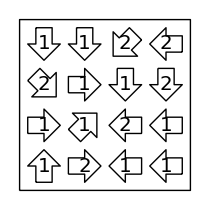

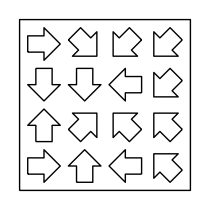

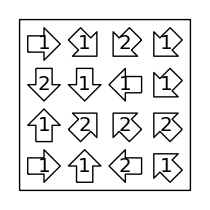

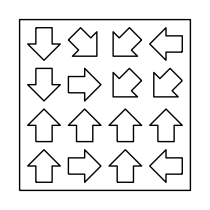

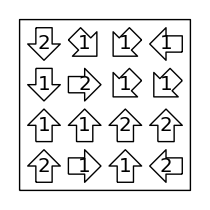

-Graphics-

-Graphics-

-Graphics-

«59 more identical outputs»

## 1-->2-->1 - 5x5

-Graphics-

-Graphics-

-Graphics-

«53 more identical outputs»

## 1-->1, 2-->2 - 4x4

-Graphics-

-Graphics-

-Graphics-

«327 more identical outputs»

## 1-->1, 2-->2 - 5x5

-Graphics-

-Graphics-

-Graphics-

«13 more identical outputs»